### Fourier Transform of sine - Gaussian

Define Functions

```mathematica
sineGaussian[t_]:=A*ⅇ^(-Γ*t^2)*Sin[2*π*Subscript[f, c]*t]
```

```mathematica
FT[f_]:=Abs[1/(√T)∫_0^T (sineGaussian[t]*ⅇ^(2*π*f*ⅈ*t))ⅆt]
```

Define constants

```mathematica
T=1;Subscript[f, c]=10;Q=1;Γ=(2*π*Subscript[f, c])/Q;A=100;
```

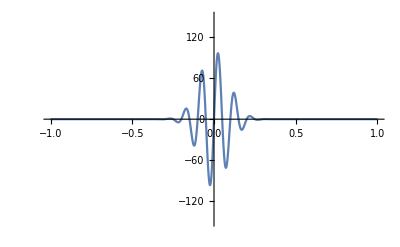

```mathematica
Plot[sineGaussian[t],{t,-1,1},PlotRange->{-150,150}]
```

If I copy the output of typing FT[f] and turn it into a new function, and plot the new function, it is significantly faster than just plotting FT[g] - this takes much longer.

```mathematica
FT[f]
```

5/2 √5 ⅇ^(-1/20 π Re[(10+f)^2]) Abs[ⅇ^(2 f π) (Erfi[1/2 (-10+f) √(π/5)]-Erfi[1/2 ((-10+20 ⅈ)+f) √(π/5)])-Erfi[1/2 (10+f) √(π/5)]+Erfi[1/2 ((10+20 ⅈ)+f) √(π/5)]]

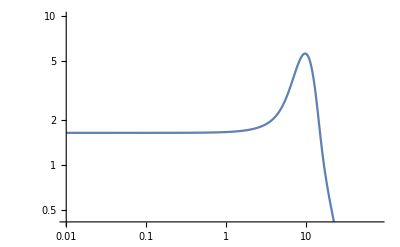

```mathematica
LogLogPlot[FT[g],{g,0.01,100},PlotRange->{0,10}] (*Much Slower!*)
```

```mathematica
new[f_]:=5/2 √5 ⅇ^(-1/20 π Re[(10+f)^2]) Abs[ⅇ^(2 f π) (Erfi[1/2 (-10+f) √(π/5)]-Erfi[1/2 ((-10+20 ⅈ)+f) √(π/5)])-Erfi[1/2 (10+f) √(π/5)]+Erfi[1/2 ((10+20 ⅈ)+f) √(π/5)]]
```

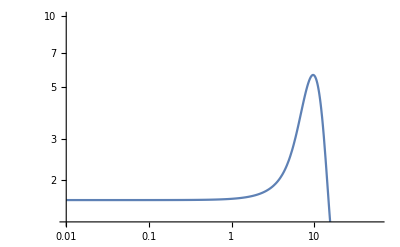

```mathematica
LogLogPlot[new[f],{f,0.01,100},PlotRange->{0,10}] (*Fast*)
```